## First the definition

```mathematica
JoinGraphs[f_,g_,h_,extra_]:=Block [
{edges,
full,
edgef=EdgeList[f],
edgeg=EdgeList[g],
edgeh=EdgeList[h],
greenEdges,
blueEdges,
greenStarts,
blueToGreen=Association[] (* gives for each blue (contract) vertex a vertex in the "with" graph *),
orangeEgdes,
todelete
},
(* greenedges are the ones connecting the with with the contract So each green starts in the "with" and ends
   in the "contract" *)
greenEdges=SetDifference[SetDifference[edgeg,edgef],edgeh];
greenStarts=Map[(blueToGreen[#[[2]]]=#[[1]];#[[1]])&,greenEdges];
blueEdges=edgeh;
edges=Join[
Table[e->Directive[{Red}],{e,edgef}],
Table[e->Directive[{Darker[Green]}],{e,greenEdges}],
Table[e->Directive[{Thick,Blue}],{e,blueEdges}]
];
orangeEgdes=Map[blueToGreen[#[[1]]]->blueToGreen[#[[2]]]&,blueEdges];
(* rewrite the orange edges *)
edges=Table[If[MemberQ[orangeEgdes,edge[[1]]],edge[[1]]->Directive[{Thick,Purple}],edge],{edge,edges}];
todelete=Map[First,Select[edges,#[[2]]==Directive[{Red}]&]];
edges=Select[edges,#[[2]]=!=Directive[{Red}]&];
	full=GraphUnion[f,g,h];


full=EdgeDelete[full,todelete];
todelete = Select[VertexList[full],VertexDegree[full,#]==0&];
If[todelete≠{},full=VertexDelete[full, todelete]];

Graph[VertexList[full],EdgeList[full],VertexLabels->Table[v->Column[{
If[SymbolLevel[v]==4,Rotate[Framed[SymbolToLabel[v],FrameStyle->If[VertexQ[h,v],Directive[Blue,Dashed],Directive[Red,Thickness[0.001]]]],Pi/6],Rotate[SymbolToLabel[v],Pi/6]]
,
}
],{v,VertexList[full]}],
EdgeStyle->edges,VertexStyle->Join[
Table[v->Red,{v,Select[VertexList[f],!MemberQ[todelete,#]&]}],
Table[v->Blue,{v,VertexList[h]}]]
]
]
```

```mathematica
DrawWithWithoutAndContract[g_,imagesize_:350]:=Block[{edges,full,implied={},mpg,  currentGraph,form,ffull,allImplied={}},
edges=EdgeList[g];
mpg=CollectMPGEdges[g];
form=DeleteDuplicates[Flatten[Table[Map[SymbolReplace[#,e]&,FindFullFormula[GContract[g,e]]],{e,Map[UndirectedEdge[#[[1]],#[[2]]]&,Subsets[VertexList[g],{2}]]}]]];
form=Table[Map[SymbolReplace[#,e]&,FindFullFormula[GContract[g,e]]],{e,EdgeList[g]}];
form=Join[form,FindFullFormula[g]];
AppendTo[form,SetsToSymbol[Table[{i},{i,VertexCount[g]}]]];
form=Sort[DeleteDuplicates[Flatten[form]],CompareSymbols];

ffull=FindFullFormula[g];
Monitor[
Table[With[{
contract =Graph[EdgeContract[g,e]]
},
With[
{
fcontract=Map[SymbolReplace[#,e]&,FindFullFormula[contract]]
},
allImplied=Join[allImplied,ImpliedNodes[fcontract,ffull]];
]
],{e,Sort[Map[SortEdge,edges]]}],
e];
Print[allImplied//Tally];
Monitor[
Table[With[{
without=Graph[EdgeDelete[g,e]],
contract =Graph[EdgeContract[g,e]],
with=Graph[g]
},
With[
{
fwithout=FindFullFormula[without],
fcontract=Map[SymbolReplace[#,e]&,FindFullFormula[contract]]
},
implied=Join[implied,ImpliedNodes[fcontract,ffull]];
currentGraph=JoinGraphs[
FormulaGraphReverse2[ffull],
FormulaGraphReverse2[fwithout],
FormulaGraphReverse2[fcontract]
];
currentGraph=Graph[
currentGraph,  ImageSize->imagesize,GraphLayout->"LayeredDigraphEmbedding", AspectRatio->1/GoldenRatio
];
Labeled[currentGraph,If[MemberQ[mpg,e],Style[e,Red],e]]
]
],{e,Sort[Map[SortEdge,edges]]}],
e]
]
```

```mathematica
Mix[head_,value_]:=Table[head[[i]]->value[[i]],{i,Length[head]}]
```

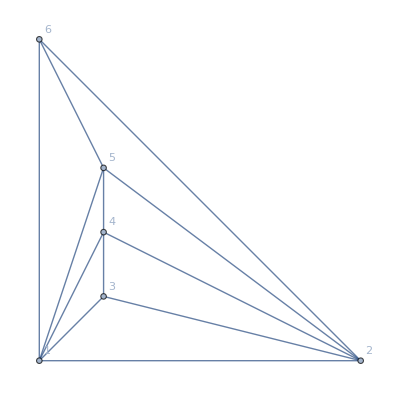
```mathematica
Mix[VertexList[-Graphics-],GraphEmbedding[-Graphics-]]
```

{1→{0.,0.},2→{5.,0.},3→{1.,1.},4→{1.,2.},5→{1.,3.},6→{0.,5.}}

{{v1x2x3x4x5x6,12},{v1x2x3x46x5,6},{v1x2x36x4x5,8},{v1x2x35x4x6,6},{v1x2x35x46,1}}

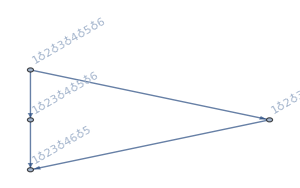
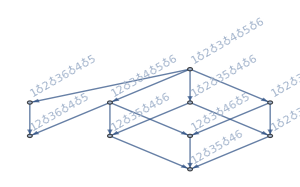
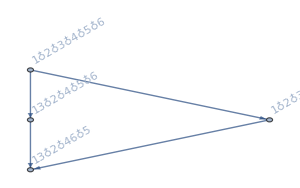
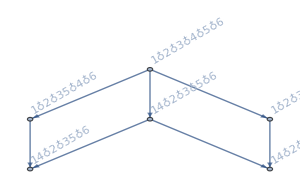
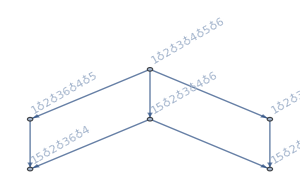
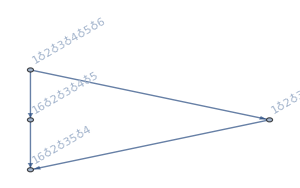
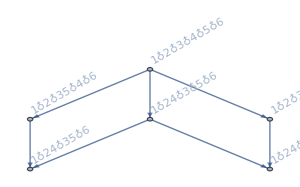
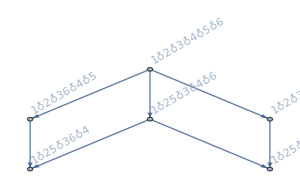
{-Graphics-2<->3,-Graphics-1<->2,-Graphics-1<->3,-Graphics-1<->4,-Graphics-1<->5,-Graphics-1<->6,-Graphics-2<->4,-Graphics-2<->5,-Graphics-2<->6,-Graphics-3<->4,-Graphics-4<->5,-Graphics-5<->6}

```mathematica
DrawWithWithoutAndContract[MinimalGraph[5],300]
```

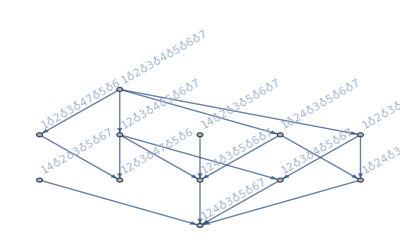
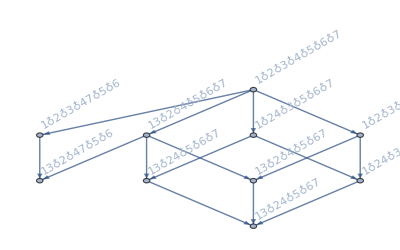
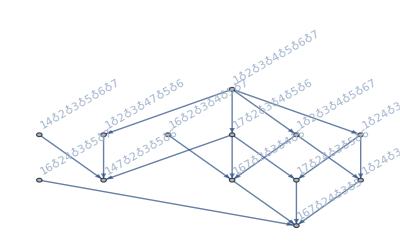
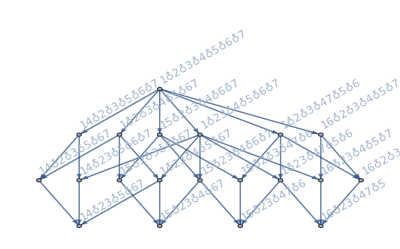
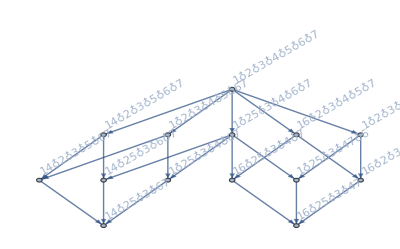
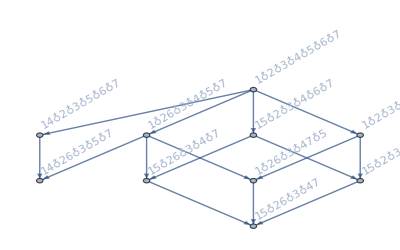
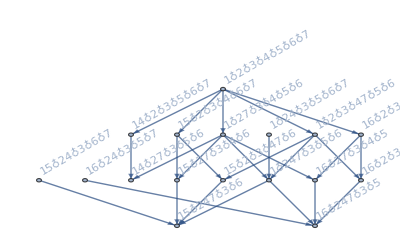
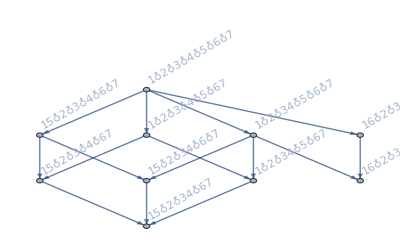
{-Graphics-1<->2,-Graphics-1<->3,-Graphics-1<->7,-Graphics-2<->3,-Graphics-2<->5,-Graphics-2<->6,-Graphics-2<->7,-Graphics-3<->4,-Graphics-3<->5,-Graphics-3<->6,-Graphics-3<->7,-Graphics-4<->5,-Graphics-4<->6,-Graphics-5<->6,-Graphics-5<->7}

```mathematica
DrawWithWithoutAndContract[ReadGrof[5],400]
```

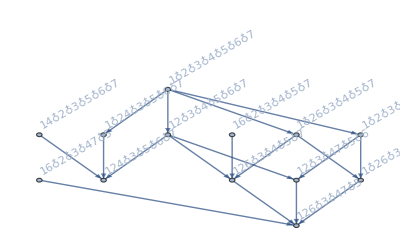
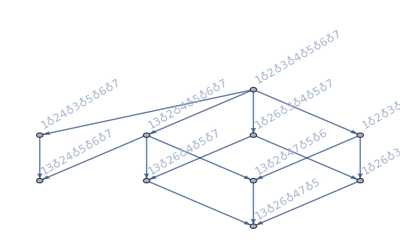
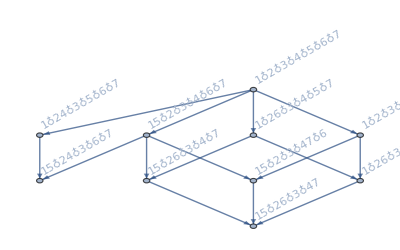
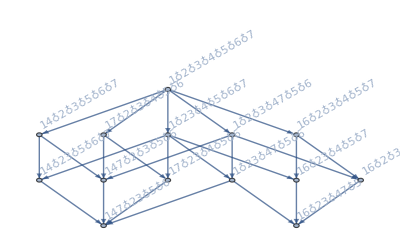
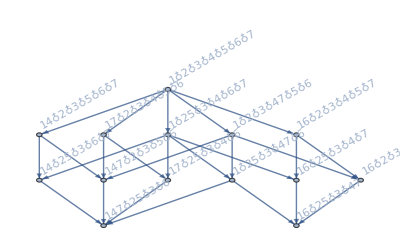
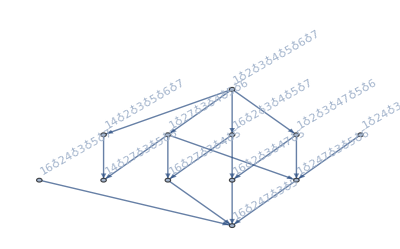
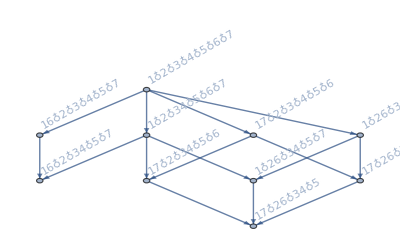
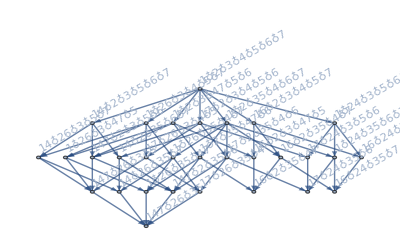
{-Graphics-1<->2,-Graphics-1<->3,-Graphics-1<->5,-Graphics-2<->3,-Graphics-2<->5,-Graphics-2<->7,-Graphics-3<->4,-Graphics-3<->5,-Graphics-3<->6,-Graphics-3<->7,-Graphics-4<->5,-Graphics-4<->6,-Graphics-5<->6,-Graphics-5<->7,-Graphics-6<->7}

```mathematica
DrawWithWithoutAndContract[ReadGrof[8],400]
```